```mathematica
Quit[];
```

```mathematica
1+1//Timing;
```

The 1 and 2 loop solution to the RG equation for C (including only QCD corrections) is:

```mathematica
<<"/Users/noahsteinberg/Desktop/BNV_Mathematica_Programs/RunDec.m"
b1[Nfl_, Ncl_]:= (-(11Ncl - 2Nfl))/3;
b2[Nfl_, Ncl_]:= -34/3 Ncl^2 + 10/3 Ncl Nfl + 2((Ncl^2 - 1)/(2  Ncl))Nfl;
Δ = -10/3;
b1[6,3]
b2[6,3]
AQCDRL1loop[MX_, mt_, MZ_, as5MZ_, p0_]:= Module[{as5mt, as6mt, as6p0, as6mx},
as5mt = AlphasExact[as5MZ, MZ, mt, 5, 4];
as6mt = DecAsUpOS[as5mt, mt, mt, 5, 4];
as6mx = AlphasExact[as6mt, mt, MX, 6, 4];
as6p0 = AlphasExact[as6mt, mt, p0, 6, 4];
Return[(as6p0/as6mx)^(-2/b1[6,3])];]
```

RunDec: a Mathematica package for running and decoupling of the

strong coupling and quark masses

by K.G. Chetyrkin, J.H. K\"uhn and M. Steinhauser (January 2000)

by F. Herren and M. Steinhauser (April 2016, v2.1)

-7

-26

```mathematica
AQCDRL2loop[MX_, mt_, MZ_, as5MZ_, p0_]:= Module[{as5mt, as6mt, as6p0,as6mx},
as5mt = AlphasExact[as5MZ, MZ, mt, 5, 4];
as6mt = DecAsUpOS[as5mt, mt, mt, 5, 4];
as6mx = AlphasExact[as6mt, mt, MX, 6, 4];
as6p0 = AlphasExact[as6mt, mt, p0, 6, 4];
Return[(as6p0/as6mx)^(-2/b1[6,3])((as6p0 + (4π(-7))/b2[6,3])/(as6mx + (4π(-7))/b2[6,3]))^(2/b1[6,3] - (42 + 24 + 9Δ)/(18b2[6,3]))];]
```

```mathematica
LR1loop = 
Plot[.00005*AQCDRL1loop[10000, 173.21, 91.1876, 0.1185, 10^logp0], {logp0,Log10[173.21], 4}, Frame->True, FrameLabel->{"log_10(μ/GeV)", "Wilson Coefficient"}, PlotStyle->{Blue}];
```

```mathematica
AQCDRL2loop[10000, 173.21, 91.1876, 0.1185, 173.21]

LR2loop = 
Plot[.00005*AQCDRL2loop[10000, 173.21, 91.1876, 0.1185, 10^logp0], {logp0, Log10[173.21], 4}, Frame->True, FrameLabel->{"log_10(μ/GeV)", "Wilson Coefficient"}, PlotStyle->{Red}];
```

1.12057

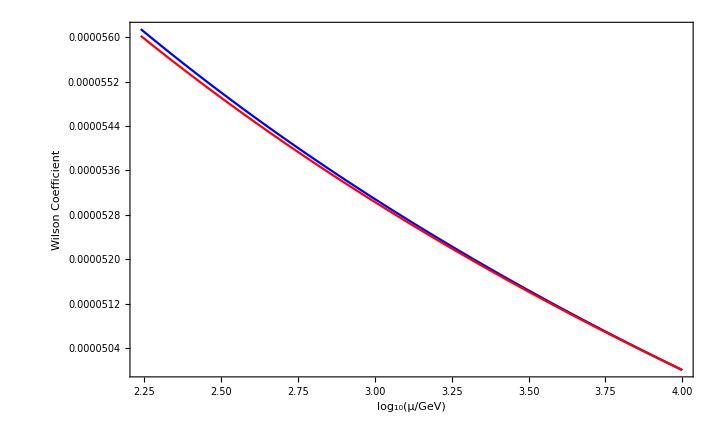

```mathematica
Show[LR1loop, LR2loop, PlotRange->All]
```